```mathematica
rhoDiscl =( (2^(l-1)Gamma[l+d/2])/(Pi^(d/2)Gamma[l+1])Gamma[d/2-delPhi]^2/Gamma[delPhi]^2 1/(Gamma[del-d/2]Gamma[d-del-d/2])(del+l-1)(d-del+l-1)Gamma[del-1]Gamma[d-del-1] ((Gamma[(l-del+2delPhi)/2]Gamma[(l-d+del+2delPhi)/2])/(Gamma[(d+l+del-2 delPhi)/2]Gamma[(d+l+d-del-2 delPhi)/2])))/.{del->d/2+I nu};
Ndel = 1/(4 Pi Pi^(d/2))Gamma[d/2-del]Gamma[del];
Kldel =(2^(2l) (Gamma[(del+l)/2]^2 Gamma[(d-del+l)/2]^2))/(l! Pochhammer[d/2-1,l]Gamma[del-d/2]Gamma[d/2-del]) (Gamma[delPhi - (del-l)/2]^2 Gamma[delPhi - (d-del-l)/2]^2)/(Pochhammer[del-1,l]Pochhammer[d-del-1,l]);
```

```mathematica
flTilde = nu/(2 Pi I)(Ndel/.{del->delPhi})^2/Gamma[delPhi]^4 Gamma[I nu]Gamma[-I nu] Sin[Pi/2(2delPhi+l-d/2-I nu)]^2(Kldel/.{del->d/2+I nu});
gamma = (Gamma[d/4+I nu/2] Gamma[d/4-I nu/2])^2 Gamma[d/4+I (nu-2 I (delPhi-d/2))/2]Gamma[d/4-I (nu-2 I (delPhi-d/2))/2]Gamma[d/4+I (nu+2 I (delPhi-d/2))/2]Gamma[d/4-I (nu+2 I (delPhi-d/2))/2](1/(64 Pi^(d/2+1)Gamma[d/2] nu^2 Gamma[I nu]Gamma[-I nu]Gamma[d/2+I nu]Gamma[d/2-I nu]))//Simplify;
```

```mathematica
alphal = (1/2 nuSig (gamma/.{nu->nuSig})(rhoDiscl/.{nu->nuSig}))((flTilde/.{nu->nuSig})+(flTilde/.{nu->-nuSig}));
betal = (I/2 nuSig (gamma/.{nu->nuSig})(rhoDiscl/.{nu->nuSig}))((flTilde/.{nu->nuSig})-(flTilde/.{nu->-nuSig}));
```

```mathematica
func= (1 + (alphal x)/(1+x^2)+betal/(1+x^2));
```

```mathematica
rule01 = {d->3,nuSig->1,delPhi->0.0000001,l->0};
rule02 = {d->3,nuSig->1,delPhi->17/12,l->0};
rule03 = {d->3,nuSig->1,delPhi->3/4,l->0};
rule04 = {d->3,nuSig->1,delPhi->1/4,l->0};
```

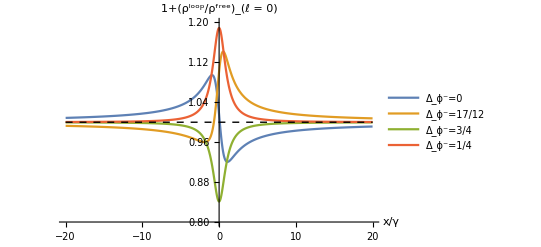

```mathematica
Plot[{func/.rule01,func/.rule02,func/.rule03,func/.rule04},{x,-20,20},Epilog->{Dashed,Line[{{-20,1},{20,1}}]},PlotRange->{{-20,20},{0.8,1.2}},AxesLabel->{"x/γ","1+(ρ^loop/ρ^free)_(ℓ = 0)"},PlotLegends->{"Δ_ϕ^-=0","Δ_ϕ^-=17/12","Δ_ϕ^-=3/4","Δ_ϕ^-=1/4"}]
```

```mathematica
rule21 = {d->3,nuSig->1,delPhi->0.00000001,l->2};
rule22 = {d->3,nuSig->1,delPhi->0.00000000+17/12,l->2};
rule23 = {d->3,nuSig->1,delPhi->0.0000000+3/4,l->2};
rule24 = {d->3,nuSig->1,delPhi->0.0000000+1/4,l->2};
```

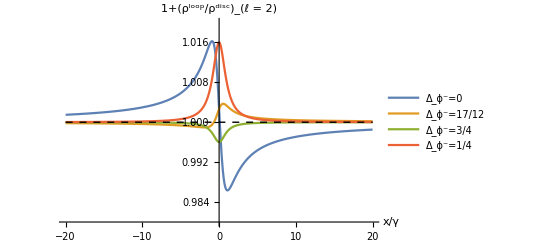

```mathematica
Plot[{func/.rule21,func/.rule22,func/.rule23,func/.rule24},{x,-20,20},Epilog->{Dashed,Line[{{-20,1},{20,1}}]},PlotRange->{{-20,20},{0.98,1.02}},AxesLabel->{"x/γ","1+(ρ^loop/ρ^disc)_(ℓ = 2)"},PlotLegends->{"Δ_ϕ^-=0","Δ_ϕ^-=17/12","Δ_ϕ^-=3/4","Δ_ϕ^-=1/4"}]
```

```mathematica
rule41 = {d->3,nuSig->1,delPhi->0.00000001,l->4};
rule42 = {d->3,nuSig->1,delPhi->0.000000+17/12,l->4};
rule43 = {d->3,nuSig->1,delPhi->0.000000+3/4,l->4};
rule44 = {d->3,nuSig->1,delPhi->0.000000+1/4,l->4};
```

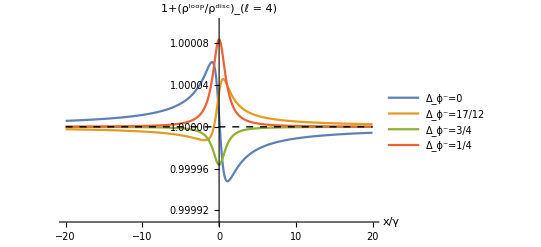

```mathematica
Plot[{func/.rule41,func/.rule42,func/.rule43,func/.rule44},{x,-20,20},Epilog->{Dashed,Line[{{-20,1},{20,1}}]},PlotRange->{{-20,20},{0.9999088,1.00010}},AxesLabel->{"x/γ","1+(ρ^loop/ρ^disc)_(ℓ = 4)"},PlotLegends->{"Δ_ϕ^-=0","Δ_ϕ^-=17/12","Δ_ϕ^-=3/4","Δ_ϕ^-=1/4"}]
```

```mathematica
Clear[nuSig,delPhi]
```

```mathematica
ruleMix1 = {d->3,nuSig -> 2, delPhi->17/12,l ->0};
ruleMix2 = {d->3,nuSig->0.793,delPhi->17/12,l->2};
ruleMix3 = {d->3,nuSig->0.0741,delPhi->17/12,l->4};
```

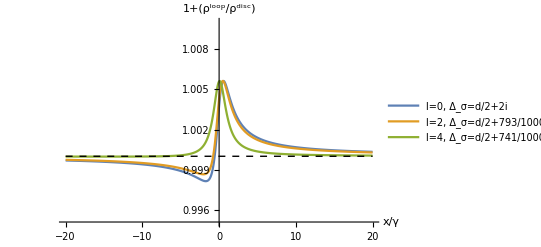

```mathematica
Plot[{func/.ruleMix1,func/.ruleMix2,func/.ruleMix3},{x,-20,20},Epilog->{Dashed,Line[{{-20,1},{20,1}}]},PlotRange->{{-20,20},{0.995088,1.01}},AxesLabel->{"x/γ","1+(ρ^loop/ρ^disc)"},PlotLegends->{"l=0, Δ_σ=d/2+2i","l=2, Δ_σ=d/2+793/1000i","l=4, Δ_σ=d/2+741/10000i"}]
```

```mathematica
ruleMix1 = {d->3,nuSig -> 2, delPhi->1/10^6,l ->0};
ruleMix2 = {d->3,nuSig->1.7,delPhi->1/10^6,l->2};
ruleMix3 = {d->3,nuSig->0.061,delPhi->1/10^6,l->4};
```

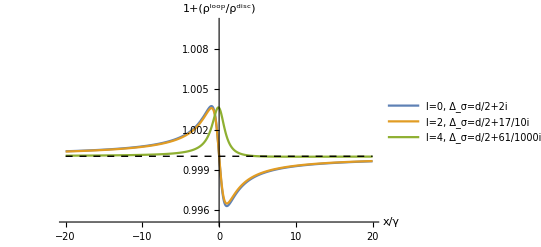

```mathematica
Plot[{func/.ruleMix1,func/.ruleMix2,func/.ruleMix3},{x,-20,20},Epilog->{Dashed,Line[{{-20,1},{20,1}}]},PlotRange->{{-20,20},{0.995088,1.01}},AxesLabel->{"x/γ","1+(ρ^loop/ρ^disc)"},PlotLegends->{"l=0, Δ_σ=d/2+2i","l=2, Δ_σ=d/2+17/10i","l=4, Δ_σ=d/2+61/1000i"}]
```

```mathematica
ruleMix1 = {d->3,nuSig -> 2, delPhi->3/4,l ->0};
ruleMix2 = {d->3,nuSig->1.7,delPhi->3/4,l->2};
ruleMix3 = {d->3,nuSig->0.091,delPhi->3/4,l->4};
```

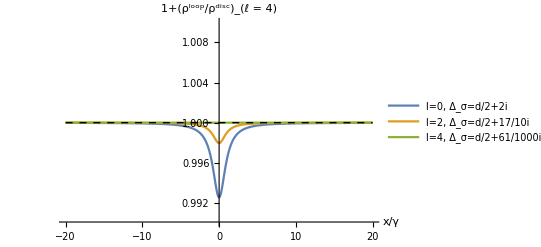

```mathematica
Plot[{func/.ruleMix1,func/.ruleMix2,func/.ruleMix3},{x,-20,20},Epilog->{Dashed,Line[{{-20,1},{20,1}}]},PlotRange->{{-20,20},{0.990088,1.01}},AxesLabel->{"x/γ","1+(ρ^loop/ρ^disc)_(ℓ = 4)"},PlotLegends->{"l=0, Δ_σ=d/2+2i","l=2, Δ_σ=d/2+17/10i","l=4, Δ_σ=d/2+61/1000i"}]
```

```mathematica
ruleMix1 = {d->3,nuSig -> 3.22, delPhi->1/10^6,l ->0};
ruleMix2 = {d->3,nuSig->03.45,delPhi->1/10^6,l->2};
ruleMix3 = {d->3,nuSig->0.74,delPhi->1/10^6,l->4};
```

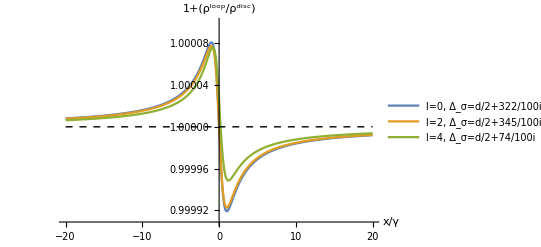

```mathematica
Plot[{func/.ruleMix1,func/.ruleMix2,func/.ruleMix3},{x,-20,20},Epilog->{Dashed,Line[{{-20,1},{20,1}}]},PlotRange->{{-20,20},{0.9999088,1.0001}},AxesLabel->{"x/γ","1+(ρ^loop/ρ^disc)"},PlotLegends->{"l=0, Δ_σ=d/2+322/100i","l=2, Δ_σ=d/2+345/100i","l=4, Δ_σ=d/2+74/100i"}]
```